```mathematica
(* Setup constants *)
```

```mathematica
EF=0.184293535388458
cs2=0.00330337980884559
cms2=0.0149317928884406
va2=0.0116669534580792
uu={1.2719770284983,-0.00116791049492655,0.000588170107640442,0.0644715584725931}
bu={0.0211076744269881,-0.000703939177500395,6.04549046091683*10^(-06),0.00687905349136715}

gcon={{-1.27502095910354,0.037833819285739,0,0},{0.037833819285739,0.0140268686134053,0,0.00243969681167397},{-0,0,0.00682571722886967,0},{-0,0.00243969681167397,0,0.0193965665211937}}
gcov=Inverse[gcon]
consts={gam->4/3,u->0.01,rho->0.1}
```

0.184294

0.00330338

0.0149318

0.011667

{1.27198,-0.00116791,0.00058817,0.0644716}

{0.0211077,-0.000703939,6.04549×10^-6,0.00687905}

{{-1.27502,0.0378338,0,0},{0.0378338,0.0140269,0,0.0024397},{0,0,0.00682572,0},{0,0.0024397,0,0.0193966}}

{{-0.724979,1.99918,0.,-0.251456},{1.99918,67.3734,0.,-8.47422},{0.,0.,146.505,0.},{-0.251456,-8.47422,0.,52.6214}}

{gam→4/3,u→0.01,rho→0.1}

```mathematica
uu={1/Sqrt[-gcov[[1,1]]],0,0,0}
```

Part::partd: Part specification gcov ⟦ 1, 1 ⟧ is longer than depth of object.

{1/(√(-gcov⟦1,1⟧)),0,0,0}

```mathematica
Sum[uu[[i]]*uu[[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]
```

Part::partd: Part specification gcov ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification gcov ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification gcov ⟦ 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

-1

```mathematica
consts={}
```

{}

```mathematica
(* Setup fluid equations *)
```

```mathematica
p=(gam-1)*u//.consts
WW=rho+u+p//.consts
bsq=Sum[bu[[i]]*bu[[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]
EF=(bsq+WW)//.consts
cms2=(va2+cs2*(1-va2))
```

0.0910895 u

rho+1.09109 u

Part::partd: Part specification bu ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification gcov ⟦ 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

bu⟦1⟧^2 gcov⟦1,1⟧+bu⟦1⟧ bu⟦2⟧ gcov⟦1,2⟧+bu⟦1⟧ bu⟦3⟧ gcov⟦1,3⟧+bu⟦1⟧ bu⟦4⟧ gcov⟦1,4⟧+bu⟦1⟧ bu⟦2⟧ gcov⟦2,1⟧+bu⟦2⟧^2 gcov⟦2,2⟧+bu⟦2⟧ bu⟦3⟧ gcov⟦2,3⟧+bu⟦2⟧ bu⟦4⟧ gcov⟦2,4⟧+bu⟦1⟧ bu⟦3⟧ gcov⟦3,1⟧+bu⟦2⟧ bu⟦3⟧ gcov⟦3,2⟧+bu⟦3⟧^2 gcov⟦3,3⟧+bu⟦3⟧ bu⟦4⟧ gcov⟦3,4⟧+bu⟦1⟧ bu⟦4⟧ gcov⟦4,1⟧+bu⟦2⟧ bu⟦4⟧ gcov⟦4,2⟧+bu⟦3⟧ bu⟦4⟧ gcov⟦4,3⟧+bu⟦4⟧^2 gcov⟦4,4⟧

rho+1.09109 u+bu⟦1⟧^2 gcov⟦1,1⟧+bu⟦1⟧ bu⟦2⟧ gcov⟦1,2⟧+bu⟦1⟧ bu⟦3⟧ gcov⟦1,3⟧+bu⟦1⟧ bu⟦4⟧ gcov⟦1,4⟧+bu⟦1⟧ bu⟦2⟧ gcov⟦2,1⟧+bu⟦2⟧^2 gcov⟦2,2⟧+bu⟦2⟧ bu⟦3⟧ gcov⟦2,3⟧+bu⟦2⟧ bu⟦4⟧ gcov⟦2,4⟧+bu⟦1⟧ bu⟦3⟧ gcov⟦3,1⟧+bu⟦2⟧ bu⟦3⟧ gcov⟦3,2⟧+bu⟦3⟧^2 gcov⟦3,3⟧+bu⟦3⟧ bu⟦4⟧ gcov⟦3,4⟧+bu⟦1⟧ bu⟦4⟧ gcov⟦4,1⟧+bu⟦2⟧ bu⟦4⟧ gcov⟦4,2⟧+bu⟦3⟧ bu⟦4⟧ gcov⟦4,3⟧+bu⟦4⟧^2 gcov⟦4,4⟧

cs2 (1-va2)+va2

```mathematica
(*Clear[bsq,va2,cs2,bu,bd,ku,kd,Kd,Ku,uu,ud,EF,WW,p,cm2]*)
```

```mathematica
(* Setup wave *)
```

```mathematica
kd=k1*{-vp,1,0,0}
ku=Table[Sum[gcon[[ii,jj]]*kd[[ii]],{ii,1,4}],{jj,1,4}]//.consts
wfl=-(kd.uu)//.consts
ksq=(kd.ku+wfl^2)//.consts
kdotva=kd.bu/Sqrt[EF]//.consts
kdotva2=kdotva^2
```

{-k1 vp,k1,0,0}

Part::partd: Part specification gcon ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification gcon ⟦ 2, 1 ⟧ is longer than depth of object.

Part::partd: Part specification gcon ⟦ 3, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

{-k1 vp gcon⟦1,1⟧+k1 gcon⟦2,1⟧,-k1 vp gcon⟦1,2⟧+k1 gcon⟦2,2⟧,-k1 vp gcon⟦1,3⟧+k1 gcon⟦2,3⟧,-k1 vp gcon⟦1,4⟧+k1 gcon⟦2,4⟧}

(k1 vp)/(√(-gcov⟦1,1⟧))

-k1 vp (-k1 vp gcon⟦1,1⟧+k1 gcon⟦2,1⟧)+k1 (-k1 vp gcon⟦1,2⟧+k1 gcon⟦2,2⟧)-(k1^2 vp^2)/gcov⟦1,1⟧

{-k1 vp,k1,0,0}.bu/(√(rho+1.09109 u+bu⟦1⟧^2 gcov⟦1,1⟧+bu⟦1⟧ bu⟦2⟧ gcov⟦1,2⟧+bu⟦1⟧ bu⟦3⟧ gcov⟦1,3⟧+bu⟦1⟧ bu⟦4⟧ gcov⟦1,4⟧+bu⟦1⟧ bu⟦2⟧ gcov⟦2,1⟧+bu⟦2⟧^2 gcov⟦2,2⟧+bu⟦2⟧ bu⟦3⟧ gcov⟦2,3⟧+bu⟦2⟧ bu⟦4⟧ gcov⟦2,4⟧+bu⟦1⟧ bu⟦3⟧ gcov⟦3,1⟧+bu⟦2⟧ bu⟦3⟧ gcov⟦3,2⟧+bu⟦3⟧^2 gcov⟦3,3⟧+bu⟦3⟧ bu⟦4⟧ gcov⟦3,4⟧+bu⟦1⟧ bu⟦4⟧ gcov⟦4,1⟧+bu⟦2⟧ bu⟦4⟧ gcov⟦4,2⟧+bu⟦3⟧ bu⟦4⟧ gcov⟦4,3⟧+bu⟦4⟧^2 gcov⟦4,4⟧))

({-k1 vp,k1,0,0}.bu)^2/(rho+1.09109 u+bu⟦1⟧^2 gcov⟦1,1⟧+bu⟦1⟧ bu⟦2⟧ gcov⟦1,2⟧+bu⟦1⟧ bu⟦3⟧ gcov⟦1,3⟧+bu⟦1⟧ bu⟦4⟧ gcov⟦1,4⟧+bu⟦1⟧ bu⟦2⟧ gcov⟦2,1⟧+bu⟦2⟧^2 gcov⟦2,2⟧+bu⟦2⟧ bu⟦3⟧ gcov⟦2,3⟧+bu⟦2⟧ bu⟦4⟧ gcov⟦2,4⟧+bu⟦1⟧ bu⟦3⟧ gcov⟦3,1⟧+bu⟦2⟧ bu⟦3⟧ gcov⟦3,2⟧+bu⟦3⟧^2 gcov⟦3,3⟧+bu⟦3⟧ bu⟦4⟧ gcov⟦3,4⟧+bu⟦1⟧ bu⟦4⟧ gcov⟦4,1⟧+bu⟦2⟧ bu⟦4⟧ gcov⟦4,2⟧+bu⟦3⟧ bu⟦4⟧ gcov⟦4,3⟧+bu⟦4⟧^2 gcov⟦4,4⟧)

```mathematica
(* pick one single dispersion relation *)
```

```mathematica
eq1=0==(1/k1^2*(-wfl^2+cs2*ksq));
```

```mathematica
(*eq1=0==(1/k1^2*(-wfl^2+kdotva2));*)
```

```mathematica
(*eq1=0==(1/k1^2*(-wfl^2+(va2+cs2*(1-va2))*ksq));*)
```

```mathematica
(* fast/slow modes *)
eq1=0==(1/k1^4*(wfl^4-wfl^2*(ksq*cms2+cs2*kdotva2)+ksq*cs2*kdotva2))
eq1=Rationalize[eq1];
```

0==1/k1^4((0.00116791 k1+1.27198 k1 vp)^4+0.0286048 (-0.000703939 k1-0.0211077 k1 vp)^2 (k1 (0.0140269 k1-0.0378338 k1 vp)+(0.00116791 k1+1.27198 k1 vp)^2-k1 vp (0.0378338 k1+1.27502 k1 vp))-(0.00116791 k1+1.27198 k1 vp)^2 (0.0286048 (-0.000703939 k1-0.0211077 k1 vp)^2+0.0149318 (k1 (0.0140269 k1-0.0378338 k1 vp)+(0.00116791 k1+1.27198 k1 vp)^2-k1 vp (0.0378338 k1+1.27502 k1 vp))))

```mathematica
(* Solve for phase speed *)
```

```mathematica
sols=Solve[eq1,vp]
```

{{vp→(cs2 gcon⟦1,2⟧ gcov⟦1,1⟧+cs2 gcon⟦2,1⟧ gcov⟦1,1⟧-√(-4 cs2 gcon⟦2,2⟧ gcov⟦1,1⟧ (1-cs2+cs2 gcon⟦1,1⟧ gcov⟦1,1⟧)+(-cs2 gcon⟦1,2⟧ gcov⟦1,1⟧-cs2 gcon⟦2,1⟧ gcov⟦1,1⟧)^2))/(2 (1-cs2+cs2 gcon⟦1,1⟧ gcov⟦1,1⟧))},{vp→(cs2 gcon⟦1,2⟧ gcov⟦1,1⟧+cs2 gcon⟦2,1⟧ gcov⟦1,1⟧+√(-4 cs2 gcon⟦2,2⟧ gcov⟦1,1⟧ (1-cs2+cs2 gcon⟦1,1⟧ gcov⟦1,1⟧)+(-cs2 gcon⟦1,2⟧ gcov⟦1,1⟧-cs2 gcon⟦2,1⟧ gcov⟦1,1⟧)^2))/(2 (1-cs2+cs2 gcon⟦1,1⟧ gcov⟦1,1⟧))}}

```mathematica
final=sols//.{gcon[[1,2]]->0,gcon[[2,1]]->0,gcov[[1,1]]->-1,gcon[[1,1]]->1,gcon[[2,2]]->1,cs2->cms^2}
```

Part::partd: Part specification gcon ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification gcon ⟦ 2, 1 ⟧ is longer than depth of object.

Part::partd: Part specification gcov ⟦ 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: "partd" will be suppressed during this calculation.

{{vp→-(√(cms^2 (1-2 cms^2)))/(1-2 cms^2)},{vp→(√(cms^2 (1-2 cms^2)))/(1-2 cms^2)}}

```mathematica
myvp=FullSimplify[final,cms2>0]
```

{{vp→-cms^2/(√(cms^2-2 cms^4))},{vp→cms^2/(√(cms^2-2 cms^4))}}

```mathematica
jonvp=C*Sqrt[1/(1-C^2)]//.{C->Sqrt[cms^2/(1-cms^2)]}
```

√(cms^2/(1-cms^2)) √(1/(1-cms^2/(1-cms^2)))

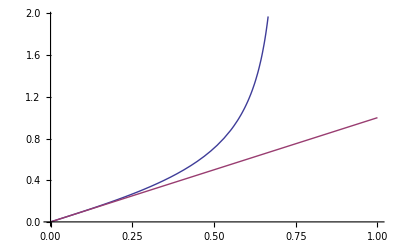

```mathematica
Plot[{jonvp,cms},{cms,0,1}]
```

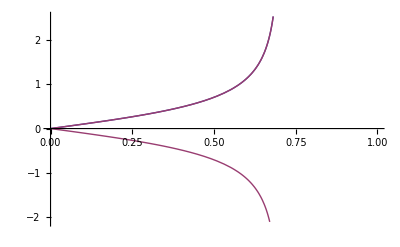

```mathematica
Plot[{jonvp,vp//.myvp},{cms,0,1}]
```

```mathematica
(* Done *)
```

```mathematica
wfl^2
```

-(k1^2 vp^2)/gcov⟦1,1⟧

```mathematica
Collect[FullSimplify[ksq/k1^2],vp]
```

vp (-gcon⟦1,2⟧-gcon⟦2,1⟧)+gcon⟦2,2⟧+vp^2 (gcon⟦1,1⟧-1/gcov⟦1,1⟧)

```mathematica
Collect[FullSimplify[kd.ku/k1^2],vp]
```

vp^2 gcon⟦1,1⟧+vp (-gcon⟦1,2⟧-gcon⟦2,1⟧)+gcon⟦2,2⟧